## OP double pass

### 2024.06.13

The MT350-A0,2-800 AOM.

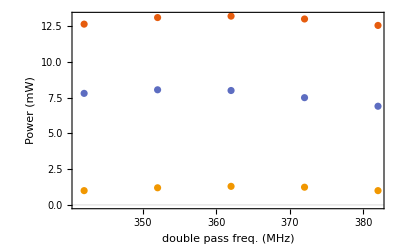

```mathematica
freqMHz={342,352,362,372,382};
singlePassmW={12.64,13.1,13.2,13,12.55};
doublePassmW={7.8,8.05,8,7.5,6.9};
inBoxmW={1,1.2,1.3,1.24,1};
ListPlot[{Transpose@{freqMHz,singlePassmW},Transpose@{freqMHz,doublePassmW},Transpose@{freqMHz,inBoxmW}},PlotTheme->"Scientific",LabelStyle->Directive[Black, FontSize->14],FrameLabel->{"double pass freq. (MHz)","Power (mW)"}]
```

single pass fit

{μ→361.053,FWHM→154.055}

double pass fit

{μ→354.313,FWHM→116.369}

fiber coupling fit

{μ→362.338,FWHM→65.1036}

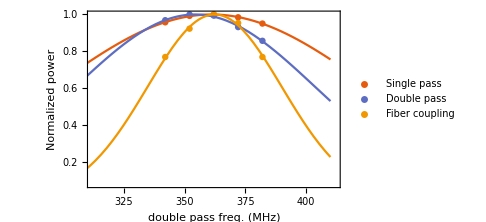

```mathematica
freqMHz={342,352,362,372,382};
singlePassmW={12.64,13.1,13.2,13,12.55};
doublePassmW={7.8,8.05,8,7.5,6.9};
inBoxmW={1,1.2,1.3,1.24,1};
model=Exp[(-(x-μ)^2)/(2(FWHM/(2√(2 Log[2])))^2)];
"single pass fit"
SPfit=FindFit[Transpose@{freqMHz,singlePassmW/Max[singlePassmW]},model,{{μ,362},{FWHM,150}},x]
"double pass fit"
DPfit=FindFit[Transpose@{freqMHz,doublePassmW/Max[doublePassmW]},model,{{μ,362},{FWHM,100}},x]
"fiber coupling fit"
Fiberfit=FindFit[Transpose@{freqMHz,inBoxmW/Max[inBoxmW]},model,{{μ,362},{FWHM,60}},x]
Show[
ListPlot[{Transpose@{freqMHz,singlePassmW/Max[singlePassmW]},Transpose@{freqMHz,doublePassmW/Max[doublePassmW]},Transpose@{freqMHz,inBoxmW/Max[inBoxmW]}},PlotTheme->"Scientific",LabelStyle->Directive[Black, FontSize->14],FrameLabel->{"double pass freq. (MHz)","Normalized power"},PlotLegends->{"Single pass","Double pass","Fiber coupling"}],
Plot[{model/.SPfit,model/.DPfit,model/.Fiberfit},{x,300,410},PlotTheme->"Scientific"],PlotRange->{{362-50,362+50},All}]
```